```mathematica
k=5;
r1=10;                 (* Radio de la órbita de la Tierra *)
r2=r1*.5;           (* Radio de la órbita de la Luna *)
v1=r1*Pi;           (* Velocidad de la Tierra *)
v2=v1*-5;     (* Velocidad de la Luna *)

(*w1=v1/r1;
w2=v2/r2;*)
w1=3;
w2=3*w1;
anguloInicial = Pi/2;
tiempo=50;

s1=NDSolve[{q'[t]==w1,q[0]==anguloInicial },{q},{t,0,tiempo}];
s2=NDSolve[{q'[t]==w2,q[0]==anguloInicial },{q},{t,0,tiempo}];
rango=r1+r2;
imgtable=Table[ParametricPlot[{{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]},{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]}},{t,0,tmax},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False],{tmax,0.1,tiempo,.5}];~Monitor~tmax

ListAnimate[imgtable]
```

C:\Users\damg1\Desktop\CIMAT DIEGO\Proyectos\imagenes\luna-densosq2.gif

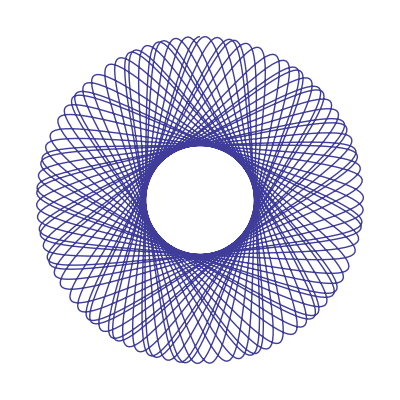

```mathematica
r1=10;                 (* Radio de la órbita de la Tierra *)
r2=r1*.5;           (* Radio de la órbita de la Luna *)
r3=r2*.5;           (* Radio de la órbita de la nave espacial *)
r4=r3*.6;           (* Radio de la órbita del astronauta *)
r5=r4*1/3;           (* Radio de la órbita del ratón *)

w1=Pi/2;
w2=w1*-Sqrt[2];
w3=w2*-6;
w4=w3*-3;
w5=w4*-5;
tiempo=150;

s1=NDSolve[{q'[t]==w1,q[0]==anguloInicial },{q},{t,0,tiempo}];
s2=NDSolve[{q'[t]==w2,q[0]==anguloInicial },{q},{t,0,tiempo}];
rango=r1+r2;

imgtable=Table[ParametricPlot[{{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]},{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]}},{t,0,tmax},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False],{tmax,0.1,tiempo,.5}];~Monitor~tmax

ListAnimate[imgtable]
Export["C:\\Users\\damg1\\Desktop\\CIMAT DIEGO\\Proyectos\\imagenes\\luna-densosq2.gif",imgtable]

ParametricPlot[{{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]}},{t,0,tiempo},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False]
```

C:\Users\damg1\Desktop\CIMAT DIEGO\Proyectos\imagenes\luna-55.gif

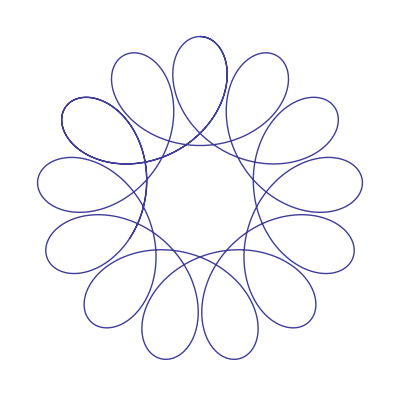

```mathematica
r1=10;                 (* Radio de la órbita de la Tierra *)
r2=r1*.5;           (* Radio de la órbita de la Luna *)
r3=r2*.5;           (* Radio de la órbita de la nave espacial *)
r4=r3*.6;           (* Radio de la órbita del astronauta *)
r5=r4*1/3;           (* Radio de la órbita del ratón *)

w1=Pi/2;
w2=w1*-5.5;
w3=w2*-6;
w4=w3*-3;
w5=w4*-5;
tiempo=9;

s1=NDSolve[{q'[t]==w1,q[0]==anguloInicial },{q},{t,0,tiempo}];
s2=NDSolve[{q'[t]==w2,q[0]==anguloInicial },{q},{t,0,tiempo}];
rango=r1+r2;

imgtable=Table[ParametricPlot[{{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]},{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]}},{t,0,tmax},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False],{tmax,0.1,tiempo,.1}];~Monitor~tmax

ListAnimate[imgtable]
Export["C:\\Users\\damg1\\Desktop\\CIMAT DIEGO\\Proyectos\\imagenes\\luna-55.gif",imgtable]

ParametricPlot[{{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]}},{t,0,tiempo},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False]
```

C:\Users\damg1\Desktop\CIMAT DIEGO\Proyectos\imagenes\nave3.gif

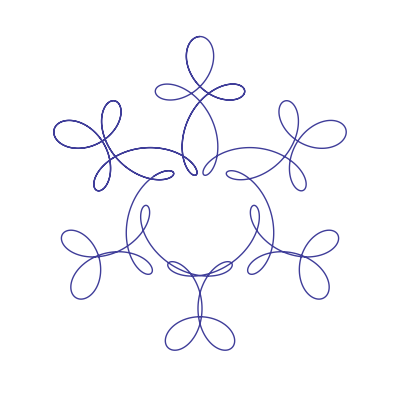

```mathematica
(* Movimiento de la NAVE ESPACIAL alrededor del Sol *)

r1=10;                 (* Radio de la órbita de la Tierra *)
r2=r1*.5;           (* Radio de la órbita de la Luna *)
r3=r2*.5;           (* Radio de la órbita de la nave espacial *)
r4=r3*.6;           (* Radio de la órbita del astronauta *)
r5=r4*1/3;           (* Radio de la órbita del ratón *)

w1=Pi/2;
w2=w1*-5;
w3=w2*-4;
w4=w3*-3;
w5=w4*-5;
anguloInicial = Pi/2;
tiempo=5;

s1=NDSolve[{q'[t]==w1,q[0]==anguloInicial },{q},{t,0,tiempo}];
s2=NDSolve[{q'[t]==w2,q[0]==anguloInicial },{q},{t,0,tiempo}];
s3=NDSolve[{q'[t]==w3,q[0]==anguloInicial },{q},{t,0,tiempo}];
rango=r1+r2+r3;
imgtable=Table[ParametricPlot[{{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]+Evaluate[{r3*Cos[q[t]],r3*Sin[q[t]]} /. s3]},{Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]}},{t,0,tmax},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False],{tmax,0.1,tiempo,.1}];~Monitor~tmax

ListAnimate[imgtable]
Export["C:\\Users\\damg1\\Desktop\\CIMAT DIEGO\\Proyectos\\imagenes\\nave3.gif",imgtable]

ParametricPlot[Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]+Evaluate[{r3*Cos[q[t]],r3*Sin[q[t]]} /. s3],{t,0,tiempo},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False]
```

C:\Users\damg1\Desktop\CIMAT DIEGO\Proyectos\imagenes\astronauta2.gif

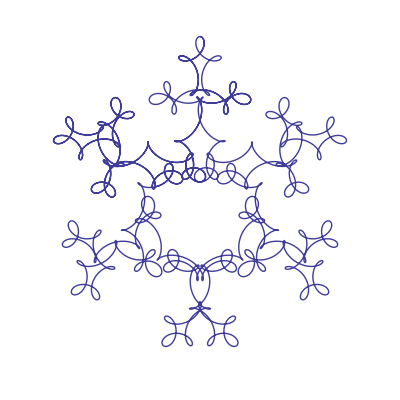

```mathematica
(* Movimiento de la ASTRONAUTA alrededor del Sol *)

r1=10;                 (* Radio de la órbita de la Tierra *)
r2=r1*.5;           (* Radio de la órbita de la Luna *)
r3=r2*.5;           (* Radio de la órbita de la nave espacial *)
r4=r3*.4;           (* Radio de la órbita del astronauta *)
r5=r4*1/3;           (* Radio de la órbita del ratón *)

w1=Pi/2;
w2=w1*-5;
w3=w2*-4;
w4=w3*-4.5;
w5=w4*-5;
anguloInicial = Pi/2;
tiempo=5;

s1=NDSolve[{q'[t]==w1,q[0]==anguloInicial },{q},{t,0,tiempo}];
s2=NDSolve[{q'[t]==w2,q[0]==anguloInicial },{q},{t,0,tiempo}];
s3=NDSolve[{q'[t]==w3,q[0]==anguloInicial },{q},{t,0,tiempo}];
s4=NDSolve[{q'[t]==w4,q[0]==anguloInicial },{q},{t,0,tiempo}];
rango=r1+r2+r3+r4;
imgtable=Table[ParametricPlot[Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]+Evaluate[{r3*Cos[q[t]],r3*Sin[q[t]]} /. s3]+Evaluate[{r4*Cos[q[t]],r4*Sin[q[t]]} /. s4],{t,0,tmax},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False],{tmax,0.1,tiempo,.08}];~Monitor~tmax

ListAnimate[imgtable]
Export["C:\\Users\\damg1\\Desktop\\CIMAT DIEGO\\Proyectos\\imagenes\\astronauta2.gif",imgtable]

ParametricPlot[Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]+Evaluate[{r3*Cos[q[t]],r3*Sin[q[t]]} /. s3]+Evaluate[{r4*Cos[q[t]],r4*Sin[q[t]]} /. s4],{t,0,tiempo},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False]
```

C:\Users\damg1\Desktop\CIMAT DIEGO\Proyectos\imagenes\raton2.gif

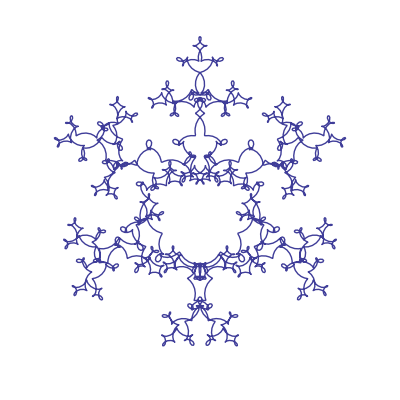

```mathematica
(* Movimiento del RATÓN alrededor del Sol *)

r1=10;                 (* Radio de la órbita de la Tierra *)
r2=r1*.5;           (* Radio de la órbita de la Luna *)
r3=r2*.5;           (* Radio de la órbita de la nave espacial *)
r4=r3*.4;           (* Radio de la órbita del astronauta *)
r5=r4*1/3;           (* Radio de la órbita del ratón *)

w1=Pi/2;
w2=w1*-5;
w3=w2*-4;
w4=w3*-4.5;
w5=w4*-4;
anguloInicial = Pi/2;
tiempo=4;

s1=NDSolve[{q'[t]==w1,q[0]==anguloInicial },{q},{t,0,tiempo}];
s2=NDSolve[{q'[t]==w2,q[0]==anguloInicial },{q},{t,0,tiempo}];
s3=NDSolve[{q'[t]==w3,q[0]==anguloInicial },{q},{t,0,tiempo}];
s4=NDSolve[{q'[t]==w4,q[0]==anguloInicial },{q},{t,0,tiempo}];
s5=NDSolve[{q'[t]==w5,q[0]==anguloInicial },{q},{t,0,tiempo}];
rango=r1+r2+r3+r4+r5;
imgtable=Table[ParametricPlot[Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]+Evaluate[{r3*Cos[q[t]],r3*Sin[q[t]]} /. s3]+Evaluate[{r4*Cos[q[t]],r4*Sin[q[t]]} /. s4]+Evaluate[{r5*Cos[q[t]],r5*Sin[q[t]]} /. s5],{t,0,tmax},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False],{tmax,0.1,tiempo,.05}];~Monitor~tmax

ListAnimate[imgtable]
Export["C:\\Users\\damg1\\Desktop\\CIMAT DIEGO\\Proyectos\\imagenes\\raton2.gif",imgtable]

ParametricPlot[Evaluate[{r1*Cos[q[t]],r1*Sin[q[t]]} /. s1]+Evaluate[{r2*Cos[q[t]],r2*Sin[q[t]]} /. s2]+Evaluate[{r3*Cos[q[t]],r3*Sin[q[t]]} /. s3]+Evaluate[{r4*Cos[q[t]],r4*Sin[q[t]]} /. s4]+Evaluate[{r5*Cos[q[t]],r5*Sin[q[t]]} /. s5],{t,0,tiempo},PlotRange->{{-rango,rango},{-rango,rango}},Axes->False]
```